## Chapter I The Very Basics

```mathematica
(*Horizontal cursor means is ready to give command*)
10!
(*evaluate the command by Shift+Enter*)
```

```mathematica
717/3
```

239

```mathematica
718/3
```

718/3

```mathematica
N[718/3](*Approximate answer*)
N[718/3,5](*round to 5 digits*)
```

239.333

239.33

WolframAlphaQueryResults(*begin with "=" to calculate free-form input, and get related clculations*)

718/3

```mathematica
a=5;(*Assign variables*)
3a+1
Clear[a](*Clear variable and make a undefined*)
Expand[(a+5)(a+9)]
Solve[2x-7==0,x](*"==" is for bool calculation while "=" is for assignment*)
```

16

45+14 a+a^2

{{x→7/2}}

WolframAlphaQueryResults

{{x→7/2}}

```mathematica
Solve[{2x-7==0,3x-2y==0},{x,y}]
```

{{x→7/2,y→21/4}}

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

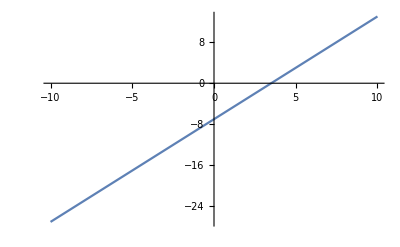

```mathematica
Plot[2x-7,{x,-10,10}]
```

WolframAlphaQueryParseResults

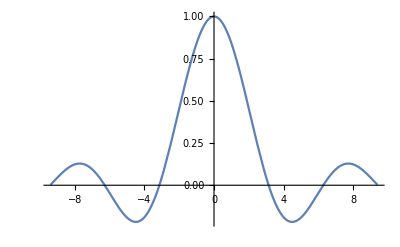

WolframAlphaQueryParseResults

-Graphics3D-

```mathematica
Table[i^2,{i,1,5}](*Table is used to create a list of values*)
```

{1,4,9,16,25}

```mathematica
Total[%](*"%" means the last output*)
```

55

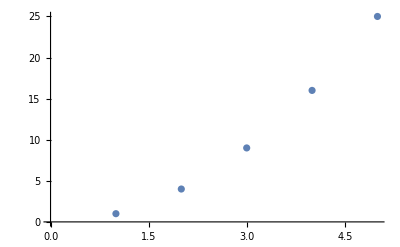

```mathematica
ListPlot[Table[i^2,{i,1,5}]](*function just like scatter*)
```

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
mat1={{1,2,3},{3,5,7},{4,6,8}};
Det[mat1]
Clear[mat1]
```

0